FittedModel[0.0213873 (1-ⅇ^(3.49809 (1.70099-x)))+0.00659957]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0213873 | 0.0000312538 | 684.311 | 1.06137614505×10^-1424
B | 0.28587 | 0.00448579 | 63.7279 | 6.9750873439×10^-368
CC | 1.70099 | 0.00429535 | 396.007 | 1.09952680641×10^-1169

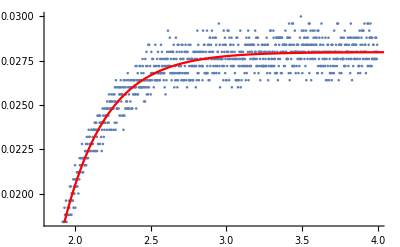

```mathematica
SetDirectory[NotebookDirectory[]];
osc=Import["../loading behaviour/ALL0011/F0011CH2.CSV", {"Data", All, {4,5}}];
nlm = NonlinearModelFit[osc[[920;;2000]], Fit[osc[[;;920]],{1},x]+A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm["ParameterTable"]
Show[ListPlot[osc[[920;;2000]]], Plot[nlm[x], {x, 1.6, 5}, PlotStyle->Red]]
```

```mathematica
Map[{#[[1]]-1.562, #[[2]]}&,osc[[782;;]]];
```

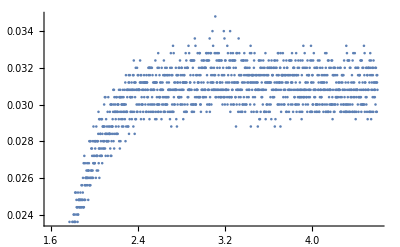

FittedModel[0.0224952 (1-ⅇ^(3.84861 (1.5373-x)))+0.008629]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0224952 | 0.0000295958 | 760.079 | 2.53497576026×10^-1940
B | 0.259834 | 0.00376052 | 69.0953 | 3.68063378666×10^-468
CC | 1.5373 | 0.00304854 | 504.276 | 1.84784107807×10^-1674

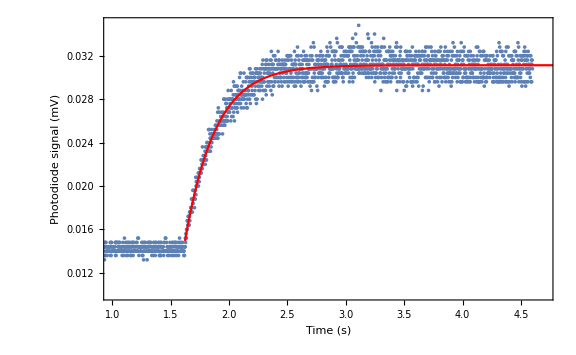

```mathematica
osc2=Import["../loading behaviour/ALL0009/F0009CH2.CSV", {"Data", All, {4,5}}];
ListPlot[osc2[[800;;2300]]]
nlm2 = NonlinearModelFit[osc2[[800;;2300]], Fit[osc2[[;;800]],{1},x]+A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm2["ParameterTable"]
Show[ListPlot[osc2[[400;;2300]]], Plot[nlm2[x], {x, 1.2, 5}, PlotStyle->Red],Frame->{{True,False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Photodiode signal (mV)",Medium]}, ImageSize->Large, PlotRange ->{{1,4.7}, {0.010, 0.035}}]
```

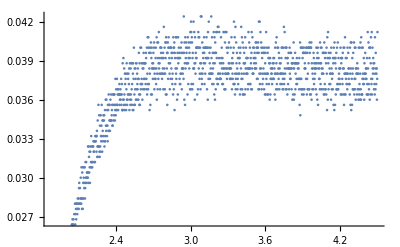

FittedModel[0.0386739 (1-ⅇ^(3.99104 («19»-x)))]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0386739 | 0.000048161 | 803.014 | 4.48950732087×10^-1764
B | 0.250561 | 0.00400334 | 62.5881 | 1.05753144852×10^-395
CC | 1.76572 | 0.00391875 | 450.583 | 4.41468058432×10^-1437

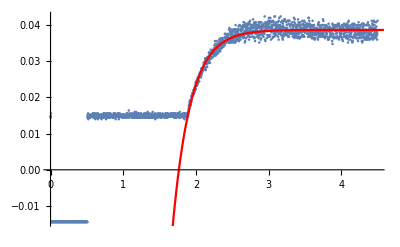

```mathematica
osc3=Import["../loading behaviour/ALL0008/F0008CH2.CSV", {"Data", All, {4,5}}];
ListPlot[osc3[[940;;2250]]]
nlm3 = NonlinearModelFit[osc3[[940;;2250]], A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm3["ParameterTable"]
Show[ListPlot[osc3[[;;2250]]], Plot[nlm3[x], {x, 0, 5}, PlotStyle->Red]]
```

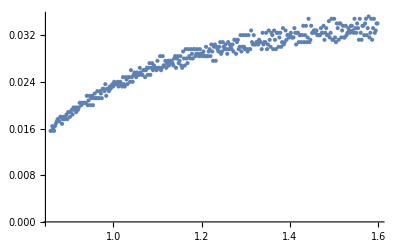

FittedModel[0.0345519 (1-ⅇ^(3.7183 («19»-x)))]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0345519 | 0.0000838172 | 412.229 | 9.71689308438×10^-1988
B | 0.26894 | 0.0121964 | 22.0508 | 5.95186×10^-97
CC | 0.698104 | 0.0139295 | 50.1168 | 2.23342746873×10^-359

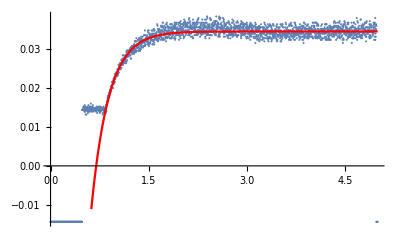

```mathematica
osc4=Import["../loading behaviour/ALL0007/F0007CH2.CSV", {"Data", All, {4,5}}];
ListPlot[osc4[[430;;800]]]
nlm4 = NonlinearModelFit[osc4[[430;;2500]], A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm4["ParameterTable"]
Show[ListPlot[osc4[[;;2500]]], Plot[nlm4[x], {x, 0, 5}, PlotStyle->Red]]
```

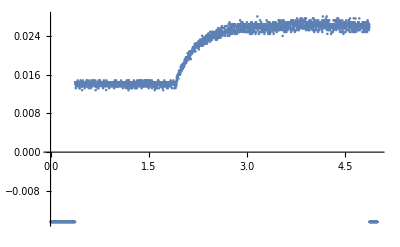

FittedModel[0.0261083 (1-ⅇ^(3.06974 («18»-x)))]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0261083 | 0.0000219679 | 1188.47 | 1.65922013838×10^-2128
B | 0.32576 | 0.00518477 | 62.8302 | 4.25975005694×10^-412
CC | 1.64839 | 0.00728334 | 226.324 | 2.85356228955×10^-1115

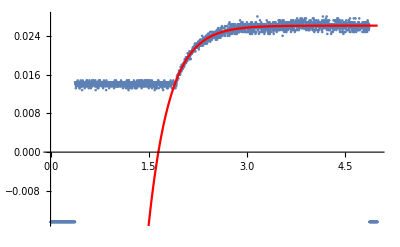

```mathematica
osc5=Import["../loading behaviour/ALL0012/F0012CH2.CSV", {"Data", All, {4,5}}];
ListPlot[osc5[[;;2500]]]
nlm5 = NonlinearModelFit[osc5[[980;;2400]], A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm5["ParameterTable"]
Show[ListPlot[osc5[[;;2500]]], Plot[nlm5[x], {x, 0, 5}, PlotStyle->Red]]
```

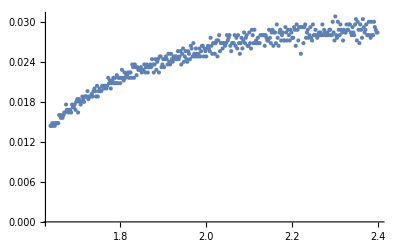

FittedModel[0.0290256 (1-ⅇ^(4.55547 («19»-x)))]

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0290256 | 0.0000262846 | 1104.28 | 4.41016996781×10^-2158
B | 0.219517 | 0.00362377 | 60.5768 | 8.0702767344×10^-403
CC | 1.49598 | 0.00427046 | 350.308 | 1.47579194962×10^-1424

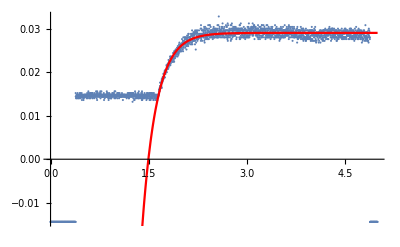

```mathematica
osc6=Import["../loading behaviour/ALL0010/F0010CH2.CSV", {"Data", All, {4,5}}];
ListPlot[osc6[[820;;1200]]]
nlm6 = NonlinearModelFit[osc6[[820;;2300]], A*(1-Exp[-(x-CC)/B]), {A,B,CC},x]
nlm6["ParameterTable"]
Show[ListPlot[osc6[[;;2500]]], Plot[nlm6[x], {x, 0, 5}, PlotStyle->Red]]
```

```mathematica
allB = {0.28587001172551046, 0.2598341098356752, 0.25056117036831693, 0.26893994818152617, 0.32576011296855106,0.21951654514526872 };
errsB={0.004485793456861757,0.0037605159463493082,0.004003335165941112,0.01219639328630999,0.005184766220281027,0.003623771121896612};
τ1=Sum[allB[[i]],{i,1,Length[allB]}]/Length[allB];
Δτ1 =Sum[errsB[[i]],{i,1,Length[errsB]}]/Length[errsB];
k = 1.38*10^(-23);
m = 1.661*10^(-27)*84.911;
v[T_] := Sqrt[3*k*T/m];
errv[T_, ΔT_] := 0.5*Sqrt[3*k/(m*T)]*ΔT;
n[T_,p_] := p/(k*T);
errn[T_,  ΔT_,p_,Δp_] := Sqrt[(p/(k*T^2))^2*ΔT^2+(1/(k*T))^2*Δp^2];
σ[τ_,Δτ_, T_, ΔT_, p_, Δp_] := {{"τ",τ},{"Δτ",Δτ},{"v",v[T]},{"v error",errv[T,ΔT]},
{"n",n[T,p]},{"n error", errn[T,ΔT,p,Δp]},{"σ",1/(τ*n[T,p]*v[T])}, {"σ error",1/(τ*n[T,p]*v[T])*Sqrt[(Δτ/τ)^2+(errv[T,ΔT]/v[T])^2+(errn[T,ΔT,p,Δp]/n[T,p])^2]}};
σ[τ1,Δτ1,293.55,0.05,8.09*10^(5-11), 0.01*10^(5-11)]
```

(τ | 0.268414
Δτ | 0.00554243
v | 293.545
v error | 0.0249996
n | 1.99704×10^15
n error | 2.49186×10^12
σ | 6.35526×10^-18
σ error | 1.31469×10^-19)